## Triangular Equilibrium

```mathematica
Clear["Global`*"]
Eqns={X'[t]==kx Z[t]-ky X[t],Y'[t]==ky X[t]-kz Y[t],Z'[t]==kz Y[t]-kx Z[t],
X[0]==x0,Y[0]==y0,Z[0]==z0
};
DSolve[Eqns,{X[t],Y[t],Z[t]},t]//Flatten;
Solution={X[t],Y[t],Z[t]}/.%;
```

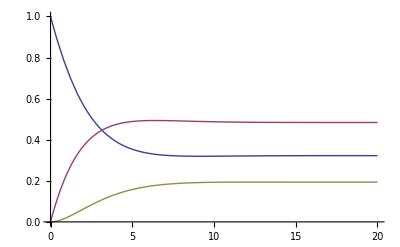

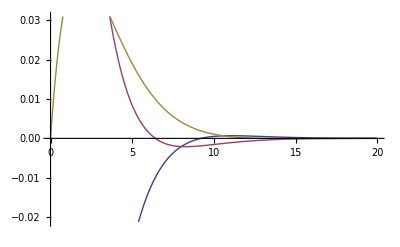

{0.322581,0.483871,0.193548}

{0.,0.,0.}

{-0.3,0.3,0}

```mathematica
Ks={kx->0.5,ky->0.3,kz->0.2};
t0={x0->1,y0->0.0,z0->0};
Soln=Chop[Solution/.Ks/.t0];
SolnD=Chop[D[Solution,t]/.Ks/.t0];
Plot[Soln,{t,0,20},PlotRange->{0,1}]
Plot[SolnD,{t,0,20},PlotRange->Automatic]
Limit[Soln,t->∞]
Limit[SolnD,t->∞]
SolnD/.t->0//Chop
```

```mathematica
Solve[{
ky x==kx z,
ky x ==kz y,
x+y+z==1
},{x,y,z}]//Flatten
%/.Ks
```

{x→(kx kz)/(kx ky+kx kz+ky kz),y→(kx ky)/(kx ky+kx kz+ky kz),z→(ky kz)/(kx ky+kx kz+ky kz)}

{x→0.322581,y→0.483871,z→0.193548}

## Competing Reactions

```mathematica
Clear["Global`*"]
DSolve[{
Y'[t]==ky X[t],
Y[0]==0,
Z'[t]==kz X[t],
Z[0]==0,
X'[t]==-(ky+kz)X[t],
X[0]==x0
},{X[t],Y[t],Z[t]},t]//Flatten
Solution=%;
```

{X[t]→ⅇ^((-ky-kz) t) x0,Y[t]→-((-1+ⅇ^((-ky-kz) t)) ky x0)/(ky+kz),Z[t]→-((-1+ⅇ^((-ky-kz) t)) kz x0)/(ky+kz)}

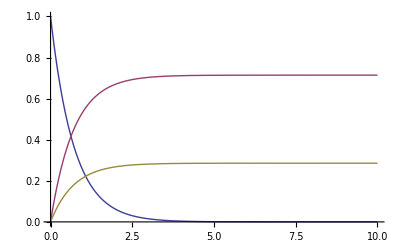

```mathematica
Soln={X[t],Y[t],Z[t]}/.Solution/.{ky->1,kz->.4,x0->1};
Plot[Soln,{t,0,10},PlotRange->{0,1}]
```

### Branching Ratio

```mathematica
Y[t]/Z[t]/.Solution
```

ky/kz

## Consecutive Reaction

```mathematica
Clear["Global`*"]
DSolve[{
X'[t]==-k1 X[t],
Y'[t]==k1 X[t]-k2 Y[t],
Z'[t]==k2 Y[t],
X[0]==x0,
Y[0]==0,
Z[0]==0
},{X[t],Y[t],Z[t]},t]//Flatten
Solution=%;
```

{X[t]→ⅇ^(-k1 t) x0,Y[t]→-(ⅇ^(-k1 t-k2 t) (-ⅇ^(k1 t)+ⅇ^(k2 t)) k1 x0)/(k1-k2),Z[t]→(ⅇ^(-k1 t-k2 t) (-ⅇ^(k1 t) k1+ⅇ^(k1 t+k2 t) k1+ⅇ^(k2 t) k2-ⅇ^(k1 t+k2 t) k2) x0)/(k1-k2)}

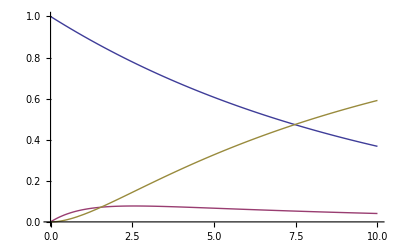

```mathematica
Soln={X[t],Y[t],Z[t]}/.Solution/.{k1->.1,k2->1,x0->1};
Plot[Soln,{t,0,10},PlotRange->{0,1}]
```

### k1>>k2

```mathematica
Y[t]/.Solution//FullSimplify
X[t]/.Solution//FullSimplify
```

-((ⅇ^(-k1 t)-ⅇ^(-k2 t)) k1 x0)/(k1-k2)

ⅇ^(-k1 t) x0

k1-k2⟶ k1

```mathematica
Y2[t_]=-((ⅇ^(-k1 t)-ⅇ^(-k2 t)) k1 x0)/k1//FullSimplify
X2[t_]=ⅇ^(-k1 t) x0/.Solution
```

(-ⅇ^(-k1 t)+ⅇ^(-k2 t)) x0

ⅇ^(-k1 t) x0

Define the constants as

```mathematica
Consts2={k1->10,k2->1,x0->1};
Soln2={X2[t],Y2[t]}/.Consts2;
```

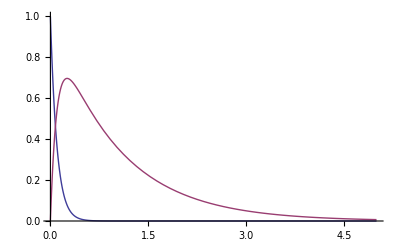

```mathematica
Plot[Soln2,{t,0,5},PlotRange->{0,1}]
```

### k2>>k1

```mathematica
Y[t]/.Solution//FullSimplify
X[t]/.Solution//FullSimplify
```

-((ⅇ^(-k1 t)-ⅇ^(-k2 t)) k1 x0)/(k1-k2)

ⅇ^(-k1 t) x0

k1-k2⟶-k2

```mathematica
Y3[t_]=(-(ⅇ^(-k1 t)-ⅇ^(-k2 t)) k1 x0)/-k2//FullSimplify
X3[t_]=ⅇ^(-k1 t) x0
```

((ⅇ^(-k1 t)-ⅇ^(-k2 t)) k1 x0)/k2

ⅇ^(-k1 t) x0

Define the constants as

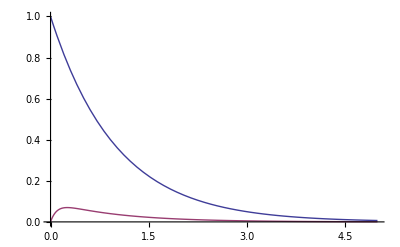

```mathematica
Consts3={k1->1,k2->10,x0->1};
Soln3={X3[t],Y3[t]}/.Consts3;
Plot[Soln3,{t,0,5},PlotRange->{0,1}]
```

### Steady State Approximation

```mathematica
DSolve[{
X'[t]==-k1 X[t],
0==k1 X[t]-k2 Y[t],
Z'[t]==k2 Y[t],
X[0]==x0,
Z[0]==0
},{X[t],Y[t],Z[t]},t]//Flatten
Solution=%;
```

{X[t]→ⅇ^(-k1 t) x0,Y[t]→(ⅇ^(-k1 t) k1 x0)/k2,Z[t]→ⅇ^(-k1 t) (-1+ⅇ^(k1 t)) x0}

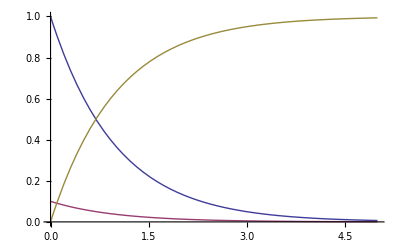

```mathematica
SolnSS={X[t],Y[t],Z[t]}/.Solution/.{k1->1,k2->10,x0->1};
Plot[SolnSS,{t,0,5}]
```